# Flow

A single function provides both hyperbolic and parabolic flows of iterated map

## Definition

```mathematica
Flow[f_,t_,x_, L_, order_:3,opts___]:= Module[{s},
Options[Flow] = {Classification -> Hyperbolic};
      classification = Classification /. {opts} /. Options[Flow];
H[0]=L;
If[classification==Hyperbolic,H[1]=f'[L]^t,H[1]=1];
mult=If[classification == Hyperbolic,f'[L],1];
Do[
H[max]=First[r[t]/.RSolve[{r[0]==0,r[t]== Sum[Derivative[k][f][L]BellY[max,k,Table[H[j]/.t->t-1,{j,max}]],{k,2,max}]+ f'[L]r[t-1]},r[t],t]];Print[max," - ",TimeUsed[]],
{max,2,order}];
s=Sum[1/k! H[k](x-L)^k,{k,0,order}]
];
```

```mathematica
flow=Flow[f,t,x, L,4,Classification->Parabolic];
```

2 - 1.048

```mathematica
flow
```

L+(-L+x) H[1]+((-1+mult^t) (-L+x)^2 H[1]^2 f''[L])/(2 (-1+mult))+1/(6 (-1+mult)^2 mult)(-L+x)^3 H[1]^3 (3 mult f''[L]^2-3 mult^(1+t) f''[L]^2-3 mult^t t f''[L]^2+3 mult^(1+t) t f''[L]^2+mult f^(3)[L]-mult^2 f^(3)[L]-mult^(1+t) f^(3)[L]+mult^(2+t) f^(3)[L])+1/(24 (-1+mult)^3 mult^2)(-L+x)^4 H[1]^4 (-15 mult^2 f''[L]^3-3 mult^(1+t) f''[L]^3+15 mult^(2+t) f''[L]^3+3 mult^(1+2 t) f''[L]^3-6 mult^t t f''[L]^3+30 mult^(1+t) t f''[L]^3-24 mult^(2+t) t f''[L]^3+6 mult^t t^2 f''[L]^3-12 mult^(1+t) t^2 f''[L]^3+6 mult^(2+t) t^2 f''[L]^3-10 mult^2 f''[L] f^(3)[L]+10 mult^3 f''[L] f^(3)[L]+10 mult^(2+t) f''[L] f^(3)[L]-10 mult^(3+t) f''[L] f^(3)[L]+10 mult^(1+t) t f''[L] f^(3)[L]-20 mult^(2+t) t f''[L] f^(3)[L]+10 mult^(3+t) t f''[L] f^(3)[L]-mult^2 f^(4)[L]+2 mult^3 f^(4)[L]-mult^4 f^(4)[L]+mult^(2+t) f^(4)[L]-2 mult^(3+t) f^(4)[L]+mult^(4+t) f^(4)[L])

```mathematica
Save["C:\\Users\\Owner\\OneDrive\\Documents\\Flow\\Flow\\parabolic.wl",flow]
```

```mathematica
Get["C:\\Users\\Owner\\OneDrive\\Documents\\Flow\\Flow\\parabolic.wl"]/.L->0;
fa=flow/.t->a;
fb=flow/.t->b;
fab=flow/.t->(a+b);
fdiff=(fa/.x->fb)-fab;
```

```mathematica
Series[fdiff,{x,0,12}]
```

O[x]^10

## Documentation

### Usage

Flow::usage = "f - function to be iterated, t - iterations, x - function vavriable, L - fixed point, order - order of series "

### Details & Options

Returns a hyperbolic flow for f^t[x] where f'[L]^n!=1  and a parabolic flow where f'[L]==1. A hyperbolic solution will go to infinity when f'[L] is a root of unity. Superattracting fixed points are not considered as they generally don't have a flow.

## Examples

### Basic Examples

The general hyperbolic solution, order is 3:

```mathematica
Flow[f,t,x, L]
```

L+(-L+x) f'[L]^t+((-L+x)^2 f'[L]^(-1+t) (-1+f'[L]^t) f''[L])/(2 (-1+f'[L]))+1/(6 (-1+f'[L])^2 (1+f'[L]))(-L+x)^3 f'[L]^(-2+t) (-1+f'[L]^t) (-3 f'[L] f''[L]^2+3 f'[L]^t f''[L]^2-f'[L] f^(3)[L]+f'[L]^2 f^(3)[L]-f'[L]^(1+t) f^(3)[L]+f'[L]^(2+t) f^(3)[L])

```mathematica
g[x_]:=(N[ⅇ^(1/ⅇ)]+z)^x;
flow=Flow[g,x,1, 0,10];
```

2 - 2.36

3 - 2.376

4 - 2.423

5 - 2.485

6 - 2.548

7 - 2.704

8 - 2.923

9 - 3.188

10 - 3.548

```mathematica
flow;
```

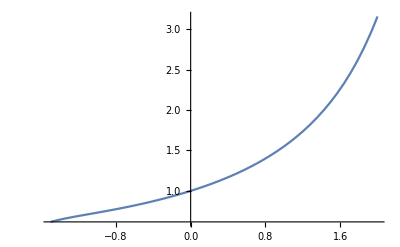

```mathematica
flowX=flow/.z->1.0;
Plot[flowX,{x,-1.5,2.}]
```

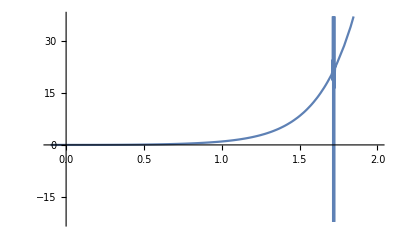

```mathematica
flowX=flow/.x->3.;
Plot[flowX,{z,-.1,2.}]
```

```mathematica
Limit[x^x,x->0]
```

1

The flow of the Sin function which is parabolic iteration. Order can go as high as 80:

```mathematica
Flow[Sin,t,x, 0,10]
```

x-(t x^3)/6+1/120 t (-4+5 t) x^5-(t (164-336 t+175 t^2) x^7)/15120+(t (-1536+4288 t-3976 t^2+1225 t^3) x^9)/362880

### Scope

Being able to take the flow of maps allows not only tetration to be extended to the complex numbers, but all the higher hyperoperators.

### Options

### Applications

### Properties and Relations

### Possible Issues

### Neat Examples

## Source & Additional Information

### Contributed By

Daniel Geisler

### Keywords

Flow

Fractional Iteration

Continuous Iteration

Hyperbolic Iteration

Parabolic Iteration

### Categories

Cloud & Deployment
 Data Manipulation & Analysis
 External Interfaces & Connections
 Geographic Data & Computation
 Graphs & Networks
 Images
 Knowledge Representation & Natural Language
 Notebook Documents & Presentation
 Repository Tools
 Social, Cultural & Linguistic Data
 Strings & Text
 System Operation & Setup
 User Interface Construction
 Wolfram Physics Project |  Core Language & Structure
 Engineering Data & Computation
 Financial Data & Computation
 Geometry
 Higher Mathematical Computation
 Just For Fun
 Machine Learning
 Programming Utilities
 Scientific and Medical Data & Computation
 Sound & Video
 Symbolic & Numeric Computation
 Time-Related Computation
 Visualization & Graphics

### Related Symbols

SymbolName (documented Wolfram Language symbol)

### Related Resource Objects

Resource Name (resources from any Wolfram repository)

### Source/Reference Citation

Source, reference or citation information

### Links

Tetration.org page on computing iterated functions and extending tetration.

### Tests

Compute and save the flow for future reference.

```mathematica
flow=Flow[f,t,x, L, 10];
hyperFile=NotebookDirectory[]<>"hyperbolic.wl";
Save[hyperFile,flow];
```

Compute and save the flow for future reference.

Show f^a[f^b[z]]-f^(a+b)[z]== 0

A flow on a set X is a group action of the additive group of real numbers on X.-Wikipedia Flow article

```mathematica
Get[hyperFile]/.L->0;
fa=flow/.t->a;
fb=flow/.t->b;
fab=flow/.t->(a+b);
fdiff=(fa/.x->fb)-fab;
```

Proof that the first nine terms are a flow.

```mathematica
Series[fdiff,{x,0,9}]
```

O[x]^10

The Flow function can return either a parabolic or hyperbolic iteration.The following Sin flow also satifies f^a[f^b[z]]-f^(a+b)[z]== 0 .

```mathematica
flow=Flow[Sin,t,x, 0,80];
```

```mathematica
sa=flow/.t->a;
sb=flow/.t->b;
sab=flow/.t->(a+b);
sdiff=(sa/.x->sb)-sab;
```

```mathematica
Series[sdiff,{x,0,80}]
```

O[x]^81

```mathematica
sinFile=NotebookDirectory[]<>"sinFlow.wl";
Save[sinFile,flow];
```

### Compatibility

#### Wolfram Language Version

13.0+

#### Operating System

Windows |  Mac |  Unix

#### Required Features

Notebooks |  Parallel Kernels |  Cloud Access

#### Environments

SessionLocal or cloud interactive session
 WebEvaluationCloud evaluation initiated by an HTTP request
 BatchJobRemote batch job |  ScriptScript run in batch mode
 WebAPIAPI called through an HTTP request
 |  SubkernelParallel or grid subkernel
 ScheduledScheduled task

#### Cloud Support

Supported in cloud

## Author Notes

Additional information about limitations, issues, etc.

## Submission Notes

Additional information for the reviewer.